```mathematica
ProductHermitian[v1_, v2_, α_, ω_,τ_]:= Conjugate[v1].{{Cos[α-ω*τ]^2+Sin[ω*τ]^2,-2 ⅈ Sin[α] Sin[ω*τ]^2},{2 ⅈ Sin[α] Sin[ω*τ]^2,Cos[α+ω*τ]^2+Sin[ω*τ]^2}}.Transpose[v2] Sec[α]^2
Evolution= {{Cos[ω*τ-α],-ⅈ*Sin[ω*τ]},{-ⅈ*Sin[ω*τ],Cos[α+ω*τ]}}*Sec[α]
EvolutionConjugated= Transpose[{{Cos[ω*τ-α],ⅈ*Sin[ω*τ]},{ⅈ*Sin[ω*τ],Cos[α+ω*τ]}}*Sec[α]]
v1Ref ={{Cos[1/4 (π-2 σ)],-ⅈ Sin[1/4 (π-2 σ)]}}
v2Ref ={{Cos[1/4 (π+2 σ)],-ⅈ Sin[1/4 (π+2 σ)]}}
v1Probe={{Cos[1/4 (π+2 δ)],-ⅈ Sin[1/4 (π+2 δ)]}}
v2Probe = {{Cos[1/4 (π+ σ)],-ⅈ*Sin[1/4 (π+σ)]*Exp[I*ϕ]}}
v3Probe = {{Cos[1/4 (π+ σ/2)],-ⅈ*Sin[1/4 (π+σ/2)]*Exp[I*ϕ]}}
```

{{Cos[α-τ ω] Sec[α],-ⅈ Sec[α] Sin[τ ω]},{-ⅈ Sec[α] Sin[τ ω],Cos[α+τ ω] Sec[α]}}

{{Cos[α-τ ω] Sec[α],ⅈ Sec[α] Sin[τ ω]},{ⅈ Sec[α] Sin[τ ω],Cos[α+τ ω] Sec[α]}}

{{Cos[1/4 (π-2 σ)],-ⅈ Sin[1/4 (π-2 σ)]}}

{{Cos[1/4 (π+2 σ)],-ⅈ Sin[1/4 (π+2 σ)]}}

{{Cos[1/4 (π+2 δ)],-ⅈ Sin[1/4 (π+2 δ)]}}

{{Cos[(π+σ)/4],-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4]}}

{{Cos[1/4 (π+σ/2)],-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)]}}

```mathematica
cosFirst=(Abs[ProductHermitian[v1Ref,v1Probe,α, ω, τ]])^2/(ProductHermitian[v1Ref,v1Ref,α, ω, τ]*ProductHermitian[v1Probe,v1Probe,α, ω, τ])
cosSecond=(Abs[ProductHermitian[v1Ref,v2Probe,α, ω, τ]])^2/(ProductHermitian[v1Ref,v1Ref,α, ω, τ]*ProductHermitian[v2Probe,v2Probe,α, ω, τ])
cosThird=(Abs[ProductHermitian[v1Ref,v3Probe,α, ω, τ]])^2/(ProductHermitian[v1Ref,v1Ref,α, ω, τ]*ProductHermitian[v3Probe,v3Probe,α, ω, τ])
```

{{(Abs[Sec[α]^2 (Cos[1/4 (π+2 δ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 Sin[α] Sin[τ ω]^2 Sin[1/4 (π-2 Conjugate[σ])])-ⅈ Sin[1/4 (π+2 δ)] (-2 ⅈ Cos[1/4 (π-2 Conjugate[σ])] Sin[α] Sin[τ ω]^2+ⅈ (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π-2 Conjugate[σ])]))]^2 Cos[α]^4)/((Cos[1/4 (π+2 δ)] (Cos[1/4 (π+2 Conjugate[δ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 Sin[α] Sin[τ ω]^2 Sin[1/4 (π+2 Conjugate[δ])])-ⅈ Sin[1/4 (π+2 δ)] (-2 ⅈ Cos[1/4 (π+2 Conjugate[δ])] Sin[α] Sin[τ ω]^2+ⅈ (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π+2 Conjugate[δ])])) (Cos[1/4 (π-2 σ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 Sin[α] Sin[τ ω]^2 Sin[1/4 (π-2 Conjugate[σ])])-ⅈ Sin[1/4 (π-2 σ)] (-2 ⅈ Cos[1/4 (π-2 Conjugate[σ])] Sin[α] Sin[τ ω]^2+ⅈ (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π-2 Conjugate[σ])])))}}

{{(Abs[Sec[α]^2 (Cos[(π+σ)/4] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 Sin[α] Sin[τ ω]^2 Sin[1/4 (π-2 Conjugate[σ])])-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (-2 ⅈ Cos[1/4 (π-2 Conjugate[σ])] Sin[α] Sin[τ ω]^2+ⅈ (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π-2 Conjugate[σ])]))]^2 Cos[α]^4)/((Cos[1/4 (π-2 σ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 Sin[α] Sin[τ ω]^2 Sin[1/4 (π-2 Conjugate[σ])])-ⅈ Sin[1/4 (π-2 σ)] (-2 ⅈ Cos[1/4 (π-2 Conjugate[σ])] Sin[α] Sin[τ ω]^2+ⅈ (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π-2 Conjugate[σ])])) (Cos[(π+σ)/4] (Cos[1/4 (π+Conjugate[σ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 ⅇ^(-ⅈ Conjugate[ϕ]) Sin[α] Sin[τ ω]^2 Sin[1/4 (π+Conjugate[σ])])-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (-2 ⅈ Cos[1/4 (π+Conjugate[σ])] Sin[α] Sin[τ ω]^2+ⅈ ⅇ^(-ⅈ Conjugate[ϕ]) (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π+Conjugate[σ])])))}}

{{(Abs[Sec[α]^2 (Cos[1/4 (π+σ/2)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 Sin[α] Sin[τ ω]^2 Sin[1/4 (π-2 Conjugate[σ])])-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (-2 ⅈ Cos[1/4 (π-2 Conjugate[σ])] Sin[α] Sin[τ ω]^2+ⅈ (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π-2 Conjugate[σ])]))]^2 Cos[α]^4)/((Cos[1/4 (π-2 σ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 Sin[α] Sin[τ ω]^2 Sin[1/4 (π-2 Conjugate[σ])])-ⅈ Sin[1/4 (π-2 σ)] (-2 ⅈ Cos[1/4 (π-2 Conjugate[σ])] Sin[α] Sin[τ ω]^2+ⅈ (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π-2 Conjugate[σ])])) (Cos[1/4 (π+σ/2)] (Cos[1/4 (π+Conjugate[σ]/2)] (Cos[α-τ ω]^2+Sin[τ ω]^2)-2 ⅇ^(-ⅈ Conjugate[ϕ]) Sin[α] Sin[τ ω]^2 Sin[1/4 (π+Conjugate[σ]/2)])-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (-2 ⅈ Cos[1/4 (π+Conjugate[σ]/2)] Sin[α] Sin[τ ω]^2+ⅈ ⅇ^(-ⅈ Conjugate[ϕ]) (Cos[α+τ ω]^2+Sin[τ ω]^2) Sin[1/4 (π+Conjugate[σ]/2)])))}}

```mathematica
cosFirstFunction[δ_,σ_,α_,ω_]:=(Abs[Sec[α]^2 (Cos[1/4 (π+2 δ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π-2 Conjugate[σ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ Sin[1/4 (π+2 δ)] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π-2 Conjugate[σ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π-2 Conjugate[σ])]))]^2 Cos[α]^4)/((Cos[1/4 (π+2 δ)] (Cos[1/4 (π+2 Conjugate[δ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π+2 Conjugate[δ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ Sin[1/4 (π+2 δ)] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π+2 Conjugate[δ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π+2 Conjugate[δ])])) (Cos[1/4 (π-2 σ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π-2 Conjugate[σ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ Sin[1/4 (π-2 σ)] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π-2 Conjugate[σ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π-2 Conjugate[σ])])))
```

```mathematica
cosSecondFunction[ϕ_,σ_,α_,ω_]:=(Abs[Sec[α]^2 (Cos[(π+σ)/4] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π-2 Conjugate[σ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π-2 Conjugate[σ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π-2 Conjugate[σ])]))]^2 Cos[α]^4)/((Cos[1/4 (π-2 σ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π-2 Conjugate[σ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ Sin[1/4 (π-2 σ)] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π-2 Conjugate[σ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π-2 Conjugate[σ])])) (Cos[(π+σ)/4] (Cos[1/4 (π+Conjugate[σ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 ⅇ^(-ⅈ Conjugate[ϕ]) Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π+Conjugate[σ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π+Conjugate[σ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ ⅇ^(-ⅈ Conjugate[ϕ]) (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π+Conjugate[σ])])))
```

```mathematica
cosThirdFunction[ϕ_,σ_,α_,ω_]:=(Abs[Sec[α]^2 (Cos[1/4 (π+σ/2)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π-2 Conjugate[σ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π-2 Conjugate[σ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π-2 Conjugate[σ])]))]^2 Cos[α]^4)/((Cos[1/4 (π-2 σ)] (Cos[1/4 (π-2 Conjugate[σ])] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π-2 Conjugate[σ])])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ Sin[1/4 (π-2 σ)] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π-2 Conjugate[σ])] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π-2 Conjugate[σ])])) (Cos[1/4 (π+σ/2)] (Cos[1/4 (π+Conjugate[σ]/2)] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 ⅇ^(-ⅈ Conjugate[ϕ]) Cos[α]^2 Cos[σ] Sin[α] Sin[1/4 (π+Conjugate[σ]/2)])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (-(2 ⅈ Cos[α]^2 Cos[σ] Cos[1/4 (π+Conjugate[σ]/2)] Sin[α])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+ⅈ ⅇ^(-ⅈ Conjugate[ϕ]) (Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2+(Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π+Conjugate[σ]/2)])))
```

```mathematica
EvolutionMT={{Cos[α+ω*τ] Sec[α],ⅈ Sec[α] Sin[ω*τ]},{ⅈ Sec[α] Sin[ω*τ],Cos[α-ω*τ] Sec[α]}}
```

{{Cos[α+τ ω] Sec[α],ⅈ Sec[α] Sin[τ ω]},{ⅈ Sec[α] Sin[τ ω],Cos[α-τ ω] Sec[α]}}

```mathematica
LeftEvolutionMT={{Cos[α+ω*τ] Sec[α],-ⅈ *Sec[α] Sin[ω*τ]},{-ⅈ *Sec[α] Sin[ω*τ],Sec[α] Cos[α-ω*τ]}}
```

{{Cos[α+τ ω] Sec[α],-ⅈ Sec[α] Sin[τ ω]},{-ⅈ Sec[α] Sin[τ ω],Cos[α-τ ω] Sec[α]}}

```mathematica
Unit={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
MatrixForm[FullSimplify[LeftEvolutionMT.EvolutionMT]]
```

(Sec[α]^2 (Cos[α+τ ω]^2+Sin[τ ω]^2) | -2 ⅈ Sec[α] Sin[τ ω]^2 Tan[α]
2 ⅈ Sec[α] Sin[τ ω]^2 Tan[α] | Sec[α]^2 (Cos[α-τ ω]^2+Sin[τ ω]^2))

```mathematica
Nm=(N0*FullSimplify[LeftEvolutionMT.EvolutionMT])
ZetaF=MatrixPower[Nm-Unit,1/2]
```

{{N0 Sec[α]^2 (Cos[α+τ ω]^2+Sin[τ ω]^2),-2 ⅈ N0 Sec[α] Sin[τ ω]^2 Tan[α]},{2 ⅈ N0 Sec[α] Sin[τ ω]^2 Tan[α],N0 Sec[α]^2 (Cos[α-τ ω]^2+Sin[τ ω]^2)}}

{{((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)),(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))},{-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)),(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))}}

```mathematica
EvolvedFirst=Evolution.Transpose[v1Probe]
EvolvedSecond=Evolution.Transpose[v2Probe]
EvolvedThird=Evolution.Transpose[v3Probe]
```

{{Cos[1/4 (π+2 δ)] Cos[α-τ ω] Sec[α]-Sec[α] Sin[1/4 (π+2 δ)] Sin[τ ω]},{-ⅈ Cos[α+τ ω] Sec[α] Sin[1/4 (π+2 δ)]-ⅈ Cos[1/4 (π+2 δ)] Sec[α] Sin[τ ω]}}

{{Cos[(π+σ)/4] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[(π+σ)/4] Sin[τ ω]},{-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[(π+σ)/4]-ⅈ Cos[(π+σ)/4] Sec[α] Sin[τ ω]}}

{{Cos[1/4 (π+σ/2)] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[1/4 (π+σ/2)] Sin[τ ω]},{-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[1/4 (π+σ/2)]-ⅈ Cos[1/4 (π+σ/2)] Sec[α] Sin[τ ω]}}

```mathematica
ZetaEvolvedFirst=ZetaF.Evolution.Transpose[v1Probe]
ZetaEvolvedSecond=ZetaF.Evolution.Transpose[v2Probe]
ZetaEvolvedThird=ZetaF.Evolution.Transpose[v3Probe]
```

{{-ⅈ Sin[1/4 (π+2 δ)] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[1/4 (π+2 δ)] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))},{Cos[1/4 (π+2 δ)] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ Sin[1/4 (π+2 δ)] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))}}

{{-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[(π+σ)/4] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))},{Cos[(π+σ)/4] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))}}

{{-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[1/4 (π+σ/2)] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))},{Cos[1/4 (π+σ/2)] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))}}

```mathematica
EvolvedFirstNormSq=Abs[EvolvedFirst[[1]][[1]]]^2+Abs[EvolvedFirst[[2]][[1]]]^2
```

Abs[-ⅈ Cos[α+τ ω] Sec[α] Sin[1/4 (π+2 δ)]-ⅈ Cos[1/4 (π+2 δ)] Sec[α] Sin[τ ω]]^2+Abs[Cos[1/4 (π+2 δ)] Cos[α-τ ω] Sec[α]-Sec[α] Sin[1/4 (π+2 δ)] Sin[τ ω]]^2

```mathematica
ZetaEvolvedFirstNormSq=Abs[ZetaEvolvedFirst[[1]][[1]]]^2+Abs[ZetaEvolvedFirst[[2]][[1]]]^2
```

(Abs[-ⅈ Sin[1/4 (π+2 δ)] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[1/4 (π+2 δ)] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2+(Abs[Cos[1/4 (π+2 δ)] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ Sin[1/4 (π+2 δ)] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2

```mathematica
DecisivenessFirst=EvolvedFirstNormSq/(EvolvedFirstNormSq+ZetaEvolvedFirstNormSq)
```

(Abs[-ⅈ Cos[α+τ ω] Sec[α] Sin[1/4 (π+2 δ)]-ⅈ Cos[1/4 (π+2 δ)] Sec[α] Sin[τ ω]]^2+Abs[Cos[1/4 (π+2 δ)] Cos[α-τ ω] Sec[α]-Sec[α] Sin[1/4 (π+2 δ)] Sin[τ ω]]^2)/(Abs[-ⅈ Cos[α+τ ω] Sec[α] Sin[1/4 (π+2 δ)]-ⅈ Cos[1/4 (π+2 δ)] Sec[α] Sin[τ ω]]^2+Abs[Cos[1/4 (π+2 δ)] Cos[α-τ ω] Sec[α]-Sec[α] Sin[1/4 (π+2 δ)] Sin[τ ω]]^2+(Abs[-ⅈ Sin[1/4 (π+2 δ)] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[1/4 (π+2 δ)] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2+(Abs[Cos[1/4 (π+2 δ)] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ Sin[1/4 (π+2 δ)] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2)

```mathematica
DecisivenessFirstFunction[δ_,σ_,α_,M0_]:=(Abs[-ⅈ Cos[1/4 (π+2 δ)] Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] Sin[1/4 (π+2 δ)]]^2+Abs[Cos[1/4 (π+2 δ)] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α]-Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π+2 δ)]]^2)/(Abs[-ⅈ Cos[1/4 (π+2 δ)] Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] Sin[1/4 (π+2 δ)]]^2+Abs[Cos[1/4 (π+2 δ)] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α]-Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π+2 δ)]]^2+(Abs[Cos[1/4 (π+2 δ)] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] (-((ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))-ⅈ (-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-((ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))) Sin[1/4 (π+2 δ)]])^2+(Abs[Cos[1/4 (π+2 δ)] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))-(ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))-ⅈ (-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))+Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))-(ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))) Sin[1/4 (π+2 δ)]])^2)
```

```mathematica
EvolvedSecondNormSq=Abs[EvolvedSecond[[1]][[1]]]^2+Abs[EvolvedSecond[[2]][[1]]]^2
ZetaEvolvedSecondNormSq=Abs[ZetaEvolvedSecond[[1]][[1]]]^2+Abs[ZetaEvolvedSecond[[2]][[1]]]^2
DecisivenessSecond=EvolvedSecondNormSq/(EvolvedSecondNormSq+ZetaEvolvedSecondNormSq)
```

Abs[-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[(π+σ)/4]-ⅈ Cos[(π+σ)/4] Sec[α] Sin[τ ω]]^2+Abs[Cos[(π+σ)/4] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[(π+σ)/4] Sin[τ ω]]^2

(Abs[-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[(π+σ)/4] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2+(Abs[Cos[(π+σ)/4] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2

(Abs[-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[(π+σ)/4]-ⅈ Cos[(π+σ)/4] Sec[α] Sin[τ ω]]^2+Abs[Cos[(π+σ)/4] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[(π+σ)/4] Sin[τ ω]]^2)/(Abs[-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[(π+σ)/4]-ⅈ Cos[(π+σ)/4] Sec[α] Sin[τ ω]]^2+Abs[Cos[(π+σ)/4] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[(π+σ)/4] Sin[τ ω]]^2+(Abs[-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[(π+σ)/4] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2+(Abs[Cos[(π+σ)/4] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ ⅇ^(ⅈ ϕ) Sin[(π+σ)/4] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2)

```mathematica
DecisivenessSecondFunction[ϕ_,σ_,α_,M0_]:=(Abs[-ⅈ Cos[(π+σ)/4] Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] Sin[(π+σ)/4]]^2+Abs[Cos[(π+σ)/4] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[(π+σ)/4]]^2)/(Abs[-ⅈ Cos[(π+σ)/4] Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] Sin[(π+σ)/4]]^2+Abs[Cos[(π+σ)/4] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[(π+σ)/4]]^2+(Abs[Cos[(π+σ)/4] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] (-((ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))-ⅈ ⅇ^(ⅈ ϕ) (-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-((ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))) Sin[(π+σ)/4]])^2+(Abs[Cos[(π+σ)/4] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))-(ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))))-ⅈ ⅇ^(ⅈ ϕ) (-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))+Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2))-(ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √(1/(2 Sin[α]-2 Cos[σ] Sin[α]^2)M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)))) Sin[(π+σ)/4]])^2)
```

```mathematica
EvolvedThirdNormSq=Abs[EvolvedThird[[1]][[1]]]^2+Abs[EvolvedThird[[2]][[1]]]^2
ZetaEvolvedThirdNormSq=Abs[ZetaEvolvedThird[[1]][[1]]]^2+Abs[ZetaEvolvedThird[[2]][[1]]]^2
DecisivenessThird=EvolvedThirdNormSq/(EvolvedThirdNormSq+ZetaEvolvedThirdNormSq)
```

Abs[-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[1/4 (π+σ/2)]-ⅈ Cos[1/4 (π+σ/2)] Sec[α] Sin[τ ω]]^2+Abs[Cos[1/4 (π+σ/2)] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[1/4 (π+σ/2)] Sin[τ ω]]^2

(Abs[-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[1/4 (π+σ/2)] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2+(Abs[Cos[1/4 (π+σ/2)] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2

(Abs[-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[1/4 (π+σ/2)]-ⅈ Cos[1/4 (π+σ/2)] Sec[α] Sin[τ ω]]^2+Abs[Cos[1/4 (π+σ/2)] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[1/4 (π+σ/2)] Sin[τ ω]]^2)/(Abs[-ⅈ ⅇ^(ⅈ ϕ) Cos[α+τ ω] Sec[α] Sin[1/4 (π+σ/2)]-ⅈ Cos[1/4 (π+σ/2)] Sec[α] Sin[τ ω]]^2+Abs[Cos[1/4 (π+σ/2)] Cos[α-τ ω] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] Sin[1/4 (π+σ/2)] Sin[τ ω]]^2+(Abs[-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (-ⅈ Sec[α] Sin[τ ω] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α+τ ω] Sec[α] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))+Cos[1/4 (π+σ/2)] (Cos[α-τ ω] Sec[α] (((-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+((4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] ((ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))-(ⅈ Cos[α] Cot[α] Csc[τ ω]^2 (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(-N0^2 (-6-2 Cos[2 α]+2 Cos[2 τ ω]-Cos[2 α-2 τ ω]-Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)) √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(32 N0 (1+Cos[2 α]) √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2+(Abs[Cos[1/4 (π+σ/2)] (-ⅈ Sec[α] Sin[τ ω] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+Cos[α-τ ω] Sec[α] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))-ⅈ ⅇ^(ⅈ ϕ) Sin[1/4 (π+σ/2)] (Cos[α+τ ω] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (4 N0-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 N0 Cos[α-τ ω]^2 Sec[α]^2-2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2-2 N0 Sec[α]^2 Sin[τ ω]^2-2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))+(√(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) (-4 N0+2 N0 Cos[2 τ ω]-N0 Cos[2 α-2 τ ω]-N0 Cos[2 α+2 τ ω]+2 N0 Cos[α-τ ω]^2 Sec[α]^2+2 N0 Cos[2 α] Cos[α-τ ω]^2 Sec[α]^2+2 N0 Sec[α]^2 Sin[τ ω]^2+2 N0 Cos[2 α] Sec[α]^2 Sin[τ ω]^2+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))/(8 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))-ⅈ Sec[α] Sin[τ ω] (-((ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]-2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2)))+(ⅈ N0 (1+Cos[2 α]) Sec[α] Sin[τ ω]^2 √(1/(1+Cos[2 α])(-2+4 N0-2 Cos[2 α]-2 N0 Cos[2 τ ω]+N0 Cos[2 α-2 τ ω]+N0 Cos[2 α+2 τ ω]+2 √2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))) Tan[α])/(2 √(N0^2 (6+2 Cos[2 α]-2 Cos[2 τ ω]+Cos[2 α-2 τ ω]+Cos[2 α+2 τ ω]) Sin[α]^2 Sin[τ ω]^2))))])^2)

```mathematica
DecisivenessThirdFunction[ϕ_,σ_,α_,M0_]:=(Abs[-ⅈ Cos[1/4 (π+σ/2)] Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] Sin[1/4 (π+σ/2)]]^2+Abs[Cos[1/4 (π+σ/2)] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π+σ/2)]]^2)/(Abs[-ⅈ Cos[1/4 (π+σ/2)] Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-ⅈ ⅇ^(ⅈ ϕ) Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] Sin[1/4 (π+σ/2)]]^2+Abs[Cos[1/4 (π+σ/2)] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α]-ⅇ^(ⅈ ϕ) Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) Sin[1/4 (π+σ/2)]]^2+(Abs[Cos[1/4 (π+σ/2)] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] (-((ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))-ⅈ ⅇ^(ⅈ ϕ) (-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-((ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(ⅈ M0 (1+Cos[2 α]) Cos[σ] Sin[α] √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))/(2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (2 Sin[α]-2 Cos[σ] Sin[α]^2)))+Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))))) Sin[1/4 (π+σ/2)]])^2+(Abs[Cos[1/4 (π+σ/2)] (Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))))-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))))-ⅈ ⅇ^(ⅈ ϕ) (-ⅈ Sec[α] √((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) ((√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(√(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(8 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))))+Cos[α+ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]] Sec[α] ((ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(ⅈ Csc[α] Sec[σ] (2 Sin[α]-2 Cos[σ] Sin[α]^2) √(1/(1+Cos[2 α])(-2+4 M0-2 Cos[2 α]+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))) (4 M0+M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2-2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √(-((M0^2 Cos[α]^2 Cos[σ] (-6-2 Cos[2 α]-Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))-(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)-(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)) (-4 M0-M0 Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-M0 Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+2 M0 Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 M0 Cos[2 α] Cos[α-ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]^2 Sec[α]^2+2 √2 √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))+(2 M0 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)+(2 M0 Cos[2 α] Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2)))/(32 M0 (1+Cos[2 α]) √((M0^2 Cos[α]^2 Cos[σ] (6+2 Cos[2 α]+Cos[2 α-2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]-2 Cos[2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]+Cos[2 α+2 ArcSin[√((Cos[α]^2 Cos[σ])/(2 Sin[α]-2 Cos[σ] Sin[α]^2))]]) Sin[α]^2)/(2 Sin[α]-2 Cos[σ] Sin[α]^2))))) Sin[1/4 (π+σ/2)]])^2)
```

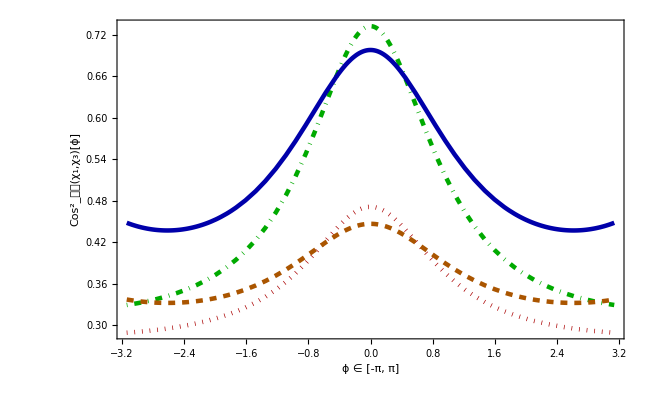

```mathematica
p1=Plot[{1-N[cosSecondFunction[-x*4/5,4/5,π/2-1,1]],1-N[cosThirdFunction[-x*4/5,4/5,π/2-1,1]],1-N[cosSecondFunction[-x*6/5,6/5,π/2-1,1]],1-N[cosThirdFunction[-x*6/5,6/5,π/2-1,1]]},{x,-π,π},PlotRange->All, PlotStyle->{Directive[Darker[Green], Thickness[0.005],DotDashed],Directive[Darker[Red], Thickness[0.005],Dotted],Directive[Darker[Blue], Thickness[0.005],Dashed[1]],Directive[Darker[Orange], Thickness[0.005],Dashed]},Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},Axes->False,FrameLabel->{"ϕ ∈ [-π, π]","(Cos^2)_𝒫𝒯(χ_1,χ_3)[ϕ]"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,GridLinesStyle->Directive[Thick,Gray]]
```

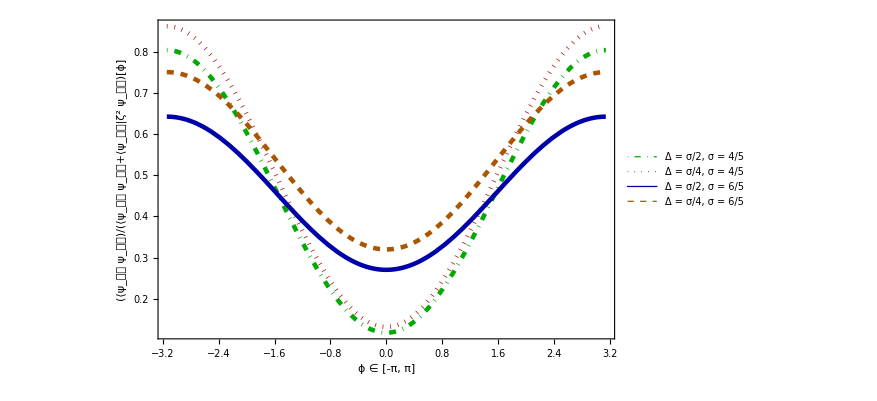

```mathematica
p2=Plot[{N[DecisivenessSecondFunction[-x,4/5,π/2-1,3]],N[DecisivenessThirdFunction[-x,4/5,π/2-1,3]],N[DecisivenessSecondFunction[-x,6/5,π/2-1,2]],N[DecisivenessThirdFunction[-x,6/5,π/2-1,2]]},{x,-π,π},PlotRange->All, PlotStyle->{Directive[Darker[Green], Thickness[0.005],DotDashed],Directive[Darker[Red], Thickness[0.005],Dotted],Directive[Darker[Blue], Thickness[0.005],Dashed[1]],Directive[Darker[Orange], Thickness[0.005],Dashed]},Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"Δ = σ/2, σ = 4/5","Δ = σ/4, σ = 4/5","Δ = σ/2, σ = 6/5","Δ = σ/4, σ = 6/5"}, LegendFunction->Framed],Axes->False, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{"ϕ ∈ [-π, π]","(⟨ψ_𝒫𝒯 ψ_𝒫𝒯)/(⟨ψ_𝒫𝒯 ψ_𝒫𝒯+⟨ψ_𝒫𝒯|ζ^2 ψ_𝒫𝒯)[ϕ]"},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,GridLinesStyle->Directive[Thick,Gray]]
```

```mathematica
title=Panel[Style["First stage, α = π/2 - 1, 𝒩(0) ≈ 𝒩_min, ϕ dependence",White,20],ImageSize->600,Background->Blue,Alignment->Center];
DependenceVariation=Deploy@Grid[{{title,SpanFromLeft},{p1,p2}},Dividers->Gray,Spacings->{0,0}]
```

First stage, α = π/2 - 1, 𝒩(0) ≈ 𝒩_min, ϕ dependence | 
-Graphics- | -Graphics-

```mathematica
Export["DependenceVariationFirst_PhiDependence.png", DependenceVariation]
```

DependenceVariationFirst_PhiDependence.png

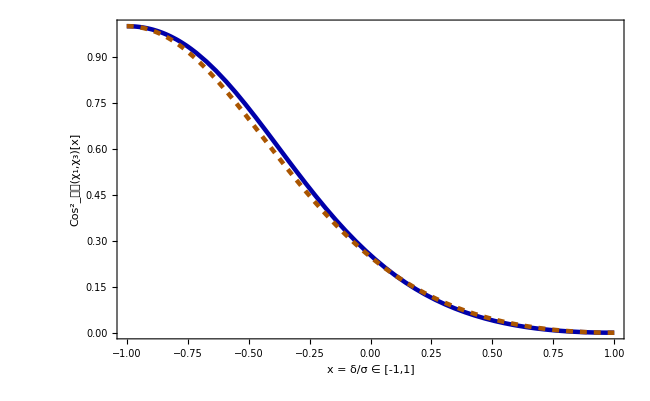

```mathematica
p1=Plot[{1-N[cosFirstFunction[-x*4/5,4/5,π/2-1,1]],1-N[cosFirstFunction[-x*6/5,6/5,π/2-1,1]]},{x,-1,1},PlotRange->All, PlotStyle->{Directive[Darker[Blue], Thickness[0.005],Dashed[1]],Directive[Darker[Orange], Thickness[0.005],Dashed]},Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},Axes->False,FrameLabel->{{"(Cos^2)_𝒫𝒯(χ_1,χ_3)[x]",},{"x = δ/σ ∈ [-1,1]",""}},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,GridLinesStyle->Directive[Thick,Gray]]
```

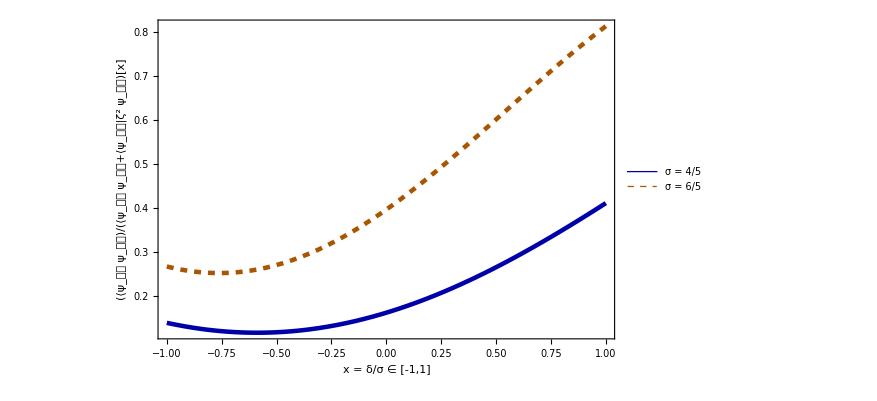

```mathematica
p2=Plot[{N[DecisivenessFirstFunction[-x*4/5,4/5,π/2-1,3]],N[DecisivenessFirstFunction[-x*6/5,6/5,π/2-1,2]]},{x,-1,1},PlotRange->All, PlotStyle->{Directive[Darker[Blue], Thickness[0.005],Dashed[1]],Directive[Darker[Orange], Thickness[0.005],Dashed]},Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large,PlotLegends-> LineLegend[{"σ = 4/5","σ = 6/5"}, LegendFunction->Framed],Axes->False, Frame->True, FrameStyle->Directive[Black,Thick], LabelStyle->Large, PlotStyle->{Directive[Darker[Green], Thickness[0.007]]},FrameLabel->{{"(⟨ψ_𝒫𝒯 ψ_𝒫𝒯)/(⟨ψ_𝒫𝒯 ψ_𝒫𝒯+⟨ψ_𝒫𝒯|ζ^2 ψ_𝒫𝒯)[x]",},{"x = δ/σ ∈ [-1,1]",""}},  LabelStyle->{FontWeight->"Bold", FontSize->25}, ImageSize->650,GridLinesStyle->Directive[Thick,Gray]]
```

```mathematica
title=Panel[Style["First stage, α = π/2 - 1, ϕ = -π/2, 𝒩(0) ≈ 𝒩_min, x dependence",White,20],ImageSize->600,Background->Blue,Alignment->Center];
DependenceVariation=Deploy@Grid[{{title,SpanFromLeft},{p1,p2}},Dividers->Gray,Spacings->{0,0}]
```

First stage, α = π/2 - 1, ϕ = -π/2, 𝒩(0) ≈ 𝒩_min, x dependence | 
-Graphics- | -Graphics-

```mathematica
Export["DependenceVariationFirst_xDependence.png", DependenceVariation]
```

DependenceVariationFirst_xDependence.png